```mathematica
$Assumptions = {Δ∈ Reals, t ∈ Reals, q ∈ Reals, q >= 0, θ ∈ Reals, δ ∈ Reals, ϕ ∈ Reals}
```

{Δ∈ℝ,t∈ℝ,q∈ℝ,q≥0,θ∈ℝ,δ∈ℝ,ϕ∈ℝ}

```mathematica
α = I t
```

ⅈ t

```mathematica
v3 =FullSimplify[ (1 - 2/3 Cos[θ + 2 π/3]^2)/(I Sqrt[2/3] Sign[Im[α]] Cos[θ + 4 π/3] - 2/3 Cos[θ] Cos[θ + 2 π/3])v1]
```

(v1 (2+Cos[1/3 (π+6 θ)]))/(-ⅈ √6 Sign[t] Sin[π/6-θ]+2 Cos[θ] Sin[π/6+θ])

```mathematica
v2 = FullSimplify[(I Sqrt[2/3] Sign[Im[α]] Cos[θ + 2 π/3] - 2/3 Cos[θ] Cos[θ + 4 π/3])/(1 - 2/3 Cos[θ]^2)v1]
```

(v1 (1+2 Cos[1/3 (π+6 θ)]-2 ⅈ √6 Sign[t] Sin[π/6+θ]))/(4-2 Cos[2 θ])

```mathematica
v1 = 1
```

1

```mathematica
ψ0v =FullSimplify[{v1, v2, v3}, Assumptions->t>0]
```

{1,(1+2 Cos[1/3 (π+6 θ)]-2 ⅈ √6 Sin[π/6+θ])/(4-2 Cos[2 θ]),(2+Cos[1/3 (π+6 θ)])/(-ⅈ √6 Sin[π/6-θ]+2 Cos[θ] Sin[π/6+θ])}

```mathematica
nm = FullSimplify[Sqrt[Conjugate[ψ0v].ψ0v]]
```

(√6)/(√(2-Cos[2 θ]))

```mathematica
ψvec = FullSimplify[ComplexExpand[ψ0v/nm]]
```

{(√(2-Cos[2 θ]))/(√6),(√6+2 √6 Cos[1/3 (π+6 θ)]-12 ⅈ Sin[π/6+θ])/(12 √(2-Cos[2 θ])),(√(2-Cos[2 θ]) (2+Cos[1/3 (π+6 θ)]) (12 ⅈ Sin[π/6-θ]+√6 (1+2 Sin[π/6+2 θ])))/(72 Sin[π/6-θ]^2+48 Cos[θ]^2 Sin[π/6+θ]^2)}

```mathematica
Clear[θ]
```

```mathematica
ψ1 = 1/Sqrt[3]{1, 1, 1}
θ = ϕ
ψ2 = FullSimplify[ComplexExpand[ψ0v/nm]]
θ = ϕ + δ
ψ3 =FullSimplify[ Normal[Series[FullSimplify[ComplexExpand[ψ0v/nm]], {δ, 0, 1}]]]
```

{1/(√3),1/(√3),1/(√3)}

ϕ

{(√(2-Cos[2 ϕ]))/(√6),(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √(2-Cos[2 ϕ])),(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2)}

δ+ϕ

{(2-Cos[2 ϕ]+δ Sin[2 ϕ])/(√6 √(2-Cos[2 ϕ])),1/(12 (2-Cos[2 ϕ])^(3/2))(-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ])),1/(12 √(2-Cos[2 ϕ]))(√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]+(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2))}

```mathematica
Clear[ϕ]
```

```mathematica
P = (Conjugate[ψ1].ψ2)/Abs[Conjugate[ψ1].ψ2] * (Conjugate[ψ2].ψ3)/Abs[Conjugate[ψ2].ψ3] * (Conjugate[ψ3].ψ1)/Abs[Conjugate[ψ3].ψ1]
```

(((√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))) (1/(12 √3)Conjugate[1/(2-Cos[2 ϕ])^(3/2)(-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ]))]+1/(12 √3)Conjugate[1/(√(2-Cos[2 ϕ]))] (√6-6 ⅈ Conjugate[Cos[ϕ]]+6 ⅈ √3 Conjugate[Sin[ϕ]]+Conjugate[(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)]+√6 Cos[2 Conjugate[ϕ]]+3 √2 Sin[2 Conjugate[ϕ]])+(Conjugate[1/(√(2-Cos[2 ϕ]))] (2-Cos[2 Conjugate[ϕ]]+Conjugate[δ] Sin[2 Conjugate[ϕ]]))/(3 √2)) ((Conjugate[√(2-Cos[2 ϕ])] (2-Cos[2 ϕ]+δ Sin[2 ϕ]))/(6 √(2-Cos[2 ϕ]))+1/(144 (2-Cos[2 ϕ])^(3/2))Conjugate[1/(√(2-Cos[2 ϕ]))] (-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ])) (√6+2 √6 Cos[1/3 (π+6 Conjugate[ϕ])]+12 ⅈ Sin[π/6+Conjugate[ϕ]])+(Conjugate[√(2-Cos[2 ϕ])] (2+Cos[1/3 (π+6 Conjugate[ϕ])]) (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]+(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)) (-12 ⅈ Sin[π/6-Conjugate[ϕ]]+√6 (1+2 Sin[π/6+2 Conjugate[ϕ]])))/(12 √(2-Cos[2 ϕ]) (72 Sin[π/6-Conjugate[ϕ]]^2+48 Conjugate[Cos[ϕ]]^2 Sin[π/6+Conjugate[ϕ]]^2))))/(Abs[(√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))] Abs[1/(12 √3)Conjugate[1/(2-Cos[2 ϕ])^(3/2)(-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ]))]+1/(12 √3)Conjugate[1/(√(2-Cos[2 ϕ]))] (√6-6 ⅈ Conjugate[Cos[ϕ]]+6 ⅈ √3 Conjugate[Sin[ϕ]]+Conjugate[(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)]+√6 Cos[2 Conjugate[ϕ]]+3 √2 Sin[2 Conjugate[ϕ]])+(Conjugate[1/(√(2-Cos[2 ϕ]))] (2-Cos[2 Conjugate[ϕ]]+Conjugate[δ] Sin[2 Conjugate[ϕ]]))/(3 √2)] Abs[(Conjugate[√(2-Cos[2 ϕ])] (2-Cos[2 ϕ]+δ Sin[2 ϕ]))/(6 √(2-Cos[2 ϕ]))+1/(144 (2-Cos[2 ϕ])^(3/2))Conjugate[1/(√(2-Cos[2 ϕ]))] (-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ])) (√6+2 √6 Cos[1/3 (π+6 Conjugate[ϕ])]+12 ⅈ Sin[π/6+Conjugate[ϕ]])+(Conjugate[√(2-Cos[2 ϕ])] (2+Cos[1/3 (π+6 Conjugate[ϕ])]) (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]+(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)) (-12 ⅈ Sin[π/6-Conjugate[ϕ]]+√6 (1+2 Sin[π/6+2 Conjugate[ϕ]])))/(12 √(2-Cos[2 ϕ]) (72 Sin[π/6-Conjugate[ϕ]]^2+48 Conjugate[Cos[ϕ]]^2 Sin[π/6+Conjugate[ϕ]]^2))])

```mathematica
ϕ = π/6
```

π/6

```mathematica
Sp = Normal[Series[P, {δ, 0, 1}]]
```

((1/(12 √3 (2-Cos[2 ϕ])^(3/2))Conjugate[-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ])]+1/(12 √3 √(2-Cos[2 ϕ]))Conjugate[(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)]+(δ Sin[2 ϕ])/(3 √2 √(2-Cos[2 ϕ]))+(5 √2-2 ⅈ √3 Cos[ϕ]-√2 Cos[2 ϕ]+6 ⅈ Sin[ϕ]+√6 Sin[2 ϕ])/(12 √(2-Cos[2 ϕ]))) (((1/6 (2-Cos[2 ϕ])-1/(144 (-2+Cos[2 ϕ]))(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]+12 ⅈ Sin[π/6+ϕ])+((2+Cos[1/3 (π+6 ϕ)]) (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]) (-12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(12 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))) ((√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))))/Abs[(√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))]+(δ (1/6 Sin[2 ϕ]+1/(144 (2-Cos[2 ϕ])^2)(√6+2 √6 Cos[1/3 (π+6 ϕ)]+12 ⅈ Sin[π/6+ϕ]) (-Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ]))+((2+Cos[1/3 (π+6 ϕ)]) ((Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)) (-12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(12 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))) ((√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))))/Abs[(√(2-Cos[2 ϕ]))/(3 √2)+(√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])/(12 √3 √(2-Cos[2 ϕ]))+(√(2-Cos[2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]) (12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(√3 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))]))/(Abs[1/(12 √3 (2-Cos[2 ϕ])^(3/2))Conjugate[-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ])]+1/(12 √3 √(2-Cos[2 ϕ]))Conjugate[(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)]+(δ Sin[2 ϕ])/(3 √2 √(2-Cos[2 ϕ]))+(5 √2-2 ⅈ √3 Cos[ϕ]-√2 Cos[2 ϕ]+6 ⅈ Sin[ϕ]+√6 Sin[2 ϕ])/(12 √(2-Cos[2 ϕ]))] Abs[1/6 (2-Cos[2 ϕ]+δ Sin[2 ϕ])+1/(144 (2-Cos[2 ϕ])^2)(√6+2 √6 Cos[1/3 (π+6 ϕ)]+12 ⅈ Sin[π/6+ϕ]) (-((-2+Cos[2 ϕ]) (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ]))-δ Sin[2 ϕ] (√6+2 √6 Cos[1/3 (π+6 ϕ)]-12 ⅈ Sin[π/6+ϕ])+4 δ (-2+Cos[2 ϕ]) Cos[π/6+ϕ] (3 ⅈ+2 √6 Sin[π/6+ϕ]))+((2+Cos[1/3 (π+6 ϕ)]) (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]+(δ Sin[2 ϕ] (√6+6 ⅈ Cos[ϕ]+√6 Cos[2 ϕ]-6 ⅈ √3 Sin[ϕ]+3 √2 Sin[2 ϕ]))/(-2+Cos[2 ϕ])-(2 δ (-2+Cos[2 ϕ]) (-3 ⅈ Cos[π/6-ϕ]+√6 Cos[π/6+2 ϕ]) (2+Cos[1/3 (π+6 ϕ)]))/(3 Sin[π/6-ϕ]^2+2 Cos[ϕ]^2 Sin[π/6+ϕ]^2)) (-12 ⅈ Sin[π/6-ϕ]+√6 (1+2 Sin[π/6+2 ϕ])))/(12 (72 Sin[π/6-ϕ]^2+48 Cos[ϕ]^2 Sin[π/6+ϕ]^2))])

```mathematica
δ=0
```

0

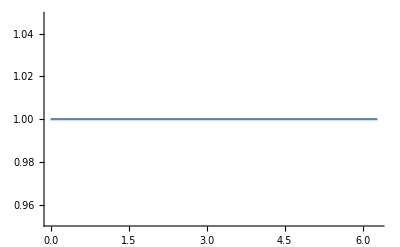

```mathematica
Plot[Sp, {ϕ, 0, 2π}]
```

```mathematica
Clear[ϕ]
```